{{Y[X]→ⅇ^(X/2) C[2] Cos[(√7 X)/2]+ⅇ^(X/2) C[1] Sin[(√7 X)/2]}}

{ⅇ^(X/2) C[2] Cos[(√7 X)/2]+ⅇ^(X/2) C[1] Sin[(√7 X)/2]}

{{Y[X]→4 ⅇ^(X/2) Cos[(√7 X)/2]-3 ⅇ^(X/2) Sin[(√7 X)/2]}}

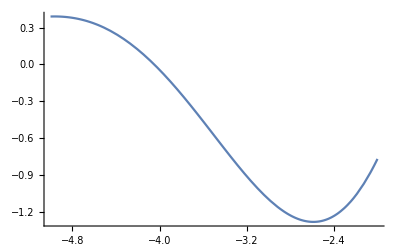

```mathematica
eqn=Y''[X]-Y'[X]+2*Y[X];
s=DSolve[eqn==0,Y[X],X]
Y[X]/. s
s1=s/. {C[1]->-3,C[2]->4}
Plot[Y[X]/. s1,{X,-2,-5}]
```

{{Y[X]→C[1] Cos[√(5/2) X]+C[2] Sin[√(5/2) X]}}

{{Y[X]→2 Cos[√(5/2) X]+√3 Sin[√(5/2) X]}}

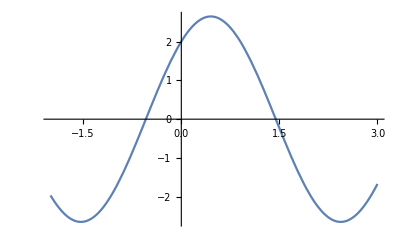

```mathematica
eqn1:= 2*Y''[X]+ 5*Y[X];
ab=DSolve[eqn1==0,Y[X],X]
a1=ab/.{C[1]-> 2, C[2]-> √3}
Plot[Y[X]/.a1,{X,-2,3}]
```